Produces animated GIFs for the solution of the 1D wave equation.
Assumes L = c = 1.

```mathematica
SetDirectory[NotebookDirectory[]];
anCoefs[f_,nmax_:100]:=Table[2 NIntegrate[f[x] Sin[n π x],{x,0,1}],{n,1,nmax}]
bnCoefs[g_,nmax_:100]:=Table[2/(n π) NIntegrate[g[x] Sin[n π x],{x,0,1}],{n,1,nmax}]
```

#### Example

```mathematica
f[x_]:= x(x^3-2 x^2+1);
g[x_]:= x(1-x);
an = anCoefs[f,100]//Quiet;
bn = bnCoefs[g,100]//Quiet;

(* I use this function "Compile" to make the evaluation of u faster *)
u = Compile[{{x,_Real},{t,_Real}},Total@Table[(an⟦n⟧ Cos[n π t] + bn⟦n⟧ Sin[n π t])Sin[n π x],{n,1,Length[an]}]
];
```

```mathematica
Animate[Plot[u[x,t],{x,0,1},
PlotRange->{-0.35,0.35}
],{t,0,3}, 
AnimationRate->0.3,
AnimationRepetitions->1,AnimationRunning->False]
```

Animate can be very heavy. I recommend you use it just for basic tests and then, to get better plots, export the outcomes as a GIF.

#### How to export as a GIF

The best way to export as a GIF is to create a list of plots and then export that list.

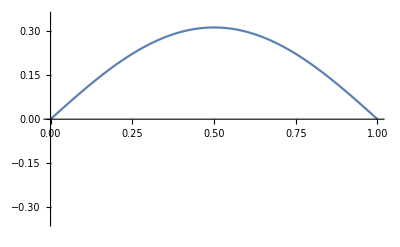
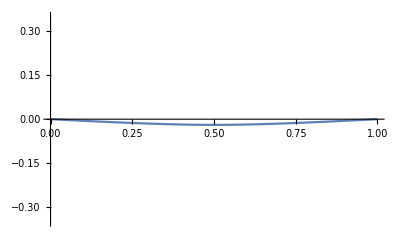
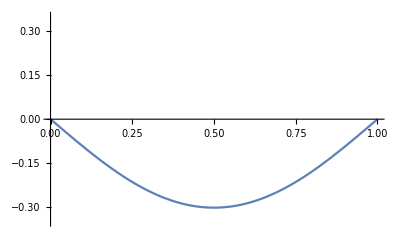
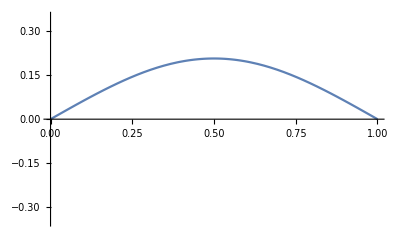
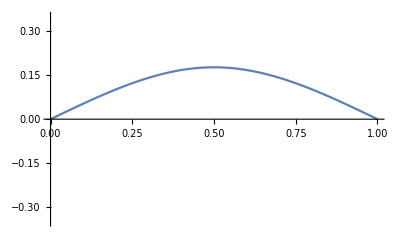
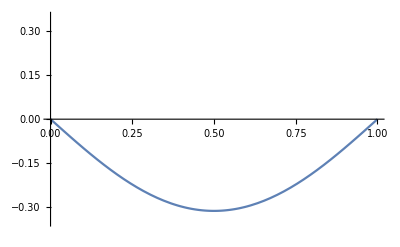

```mathematica
plots = Table[Plot[u[x,t],{x,0,1},
PlotRange->{-0.35,0.35},
FrameLabel->{"x","u"}
],{t,N@Subdivide[0,3,50]}]
```

```mathematica
Export["PDEs_wave1d_example.gif",plots,ImageResolution->150]
```

PDEs_wave1d_example.gif

### Example gallery

#### Plucked string

```mathematica
a = 0.7;
f[x_]:= Piecewise[{{x/a,0≤x≤a},{(1-x)/(1-a),a≤x≤1}}];
g[x_]:= 0;
an = anCoefs[f,100]//Quiet;
bn = bnCoefs[g,100]//Quiet;
u = Compile[{{x,_Real},{t,_Real}},Total@Table[(an⟦n⟧ Cos[n π t] + bn⟦n⟧ Sin[n π t])Sin[n π x],{n,1,Length[an]}]
];
```

```mathematica
plots = Table[Plot[u[x,t],{x,0,1},
PlotRange->{-1,1},
FrameLabel->{"x","u"}
],{t,N@Subdivide[0,3,50]}];
Export["PDEs_wave1d_plucked.gif",plots];
```

```mathematica
a = 0.7;
f[x_]:= Piecewise[{{x/a,0≤x≤a},{(1-x)/(1-a),a≤x≤1}}];
F = Interpolation[Table[{x,f[x]},{x,0,1,0.1}],InterpolationOrder->3]
```

InterpolatingFunction[…]

#### Gaussian wave-packet

```mathematica
x0 = 0.5;
σ = 0.02;
f[x_]:= Exp[-(x-x0)^2/(2 σ^2)]
g[x_]:= 0;
an = anCoefs[f,100]//Quiet;
bn = bnCoefs[g,100]//Quiet;
u = Compile[{{x,_Real},{t,_Real}},Total@Table[(an⟦n⟧ Cos[n π t] + bn⟦n⟧ Sin[n π t])Sin[n π x],{n,1,Length[an]}]
];
```

```mathematica
plots = Table[Plot[u[x,t],{x,0,1},
PlotRange->{-1,1},
FrameLabel->{"x","u"}
],{t,linspace[0,3,50]}];
Export["PDEs_wave1d_gaussian.gif",plots];
```

### URLs para acessar esse notebook

https://www.wolframcloud.com/obj/gtlandi/Published/WaveEquation_Annimated_GIFs.nb

Embedding: 
<iframe src=”https://www.wolframcloud.com/obj/gtlandi/Published/WaveEquation_Annimated_GIFs.nb?_embed=iframe” width=”600” height=”800”></iframe>